Comments: Need to help a bit in the exercise with the masses. A Hint to c) would be enough probably.

## General Setup

```mathematica
ClearAll[f,g];
f[i_,m_]:=f[i,m]=2N@NIntegrate[Cos[x i]/(4π √(m^2+2(1-Cos[x]))),{x,0,π},WorkingPrecision->20,PrecisionGoal->10,MaxRecursion->20];
g[i_,m_]:=g[i,m]=2N@NIntegrate[Cos[x i]/(4π)√(m^2+2(1-Cos[x])),{x,0,π},WorkingPrecision->20,PrecisionGoal->10,MaxRecursion->20];
```

```mathematica
ClearAll[X,P,c,s]
X[R_,m_]:=X[R,m]=Table[f[Abs[i-j],m],{i,R},{j,R}]
P[R_,m_]:=P[R,m]=Table[g[Abs[i-j],m],{i,R},{j,R}]
c[R_,m_]:=c[R,m]=√Eigenvalues[X[R,m].P[R,m]]
s[R_,m_]:=s[R,m]=(c[R,m]+1/2)Log[c[R,m]+1/2]-(c[R,m]-1/2)Log[c[R,m]-1/2]/.Indeterminate->0//Total//Re//Chop;
```

```mathematica
ClearAll[tb]
tb[Rmax_,m_]:=tb[Rmax,m]=Monitor[Table[{m R,s[R,m]},{R,1,Rmax}],R]
```

## IR and 1/3 Log(1/m)

```mathematica
masses={10^-1,5 10^-2,10^-2,5 10^-3,10^-3};
```

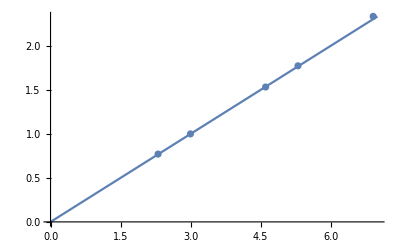

```mathematica
Dynamic[m]
Show[Plot[x/3,{x,0,7}],ListPlot@Table[{Log[1/m],Fit[tb[300,m]//Take[#,-150]&,{1,1/R,1/R^2},R]//Limit[#,R->∞]&},{m,masses}]]
```

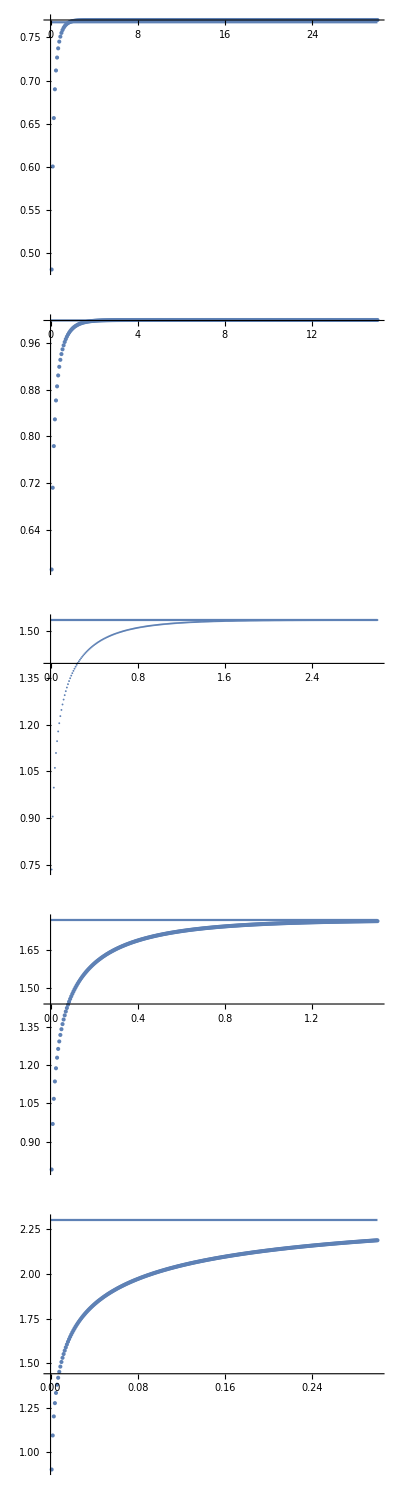

```mathematica
Monitor[tbPlots=Table[Show[ListPlot@tb[300,m],Plot[-1/3Log[m],{x,0,300 m}],PlotRange->All],{m,masses}],m]//TableForm
```

Less sofisticated:

```mathematica
tb[300,10^-2]//Last
```

{3,1.53494}

```mathematica
-1/3 Log[10^-2]//N
```

1.53506

## 1/3 Log(R) in the UV limit

```mathematica
masses={10^-2,10^-3,10^-4,10^-5,10^-6,10^-7,10^-8,10^-9};
```

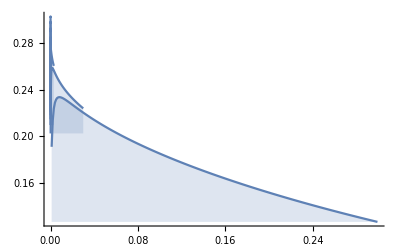

```mathematica
Table[plot[m]=Table[{tb[300,m]⟦i,1⟧,1/m tb[300,m]⟦i,1⟧(tb[300,m]⟦i+1,2⟧-tb[300,m]⟦i,2⟧)},{i,Length@tb[300,m]-1}]//ListPlot[#,Joined->True, Filling->Bottom, PlotRange->All]&,{m,masses}]//Drop[#,1]&//Show[#,PlotRange->All]&
```

Plot easier to visualize:

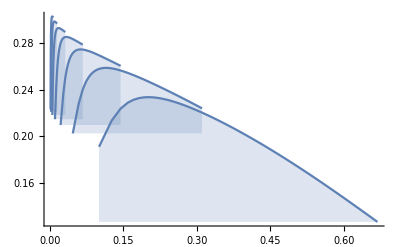

```mathematica
Table[plot[m]=Table[{(tb[300,m]⟦i,1⟧)^(1/3),1/m tb[300,m]⟦i,1⟧(tb[300,m]⟦i+1,2⟧-tb[300,m]⟦i,2⟧)},{i,Length@tb[300,m]-1}]//ListPlot[#,Joined->True, Filling->Bottom,PlotRange->All]&,{m,masses}]//Drop[#,1]&//Show[#,PlotRange->All]&
```

Another plot easier to visualize:

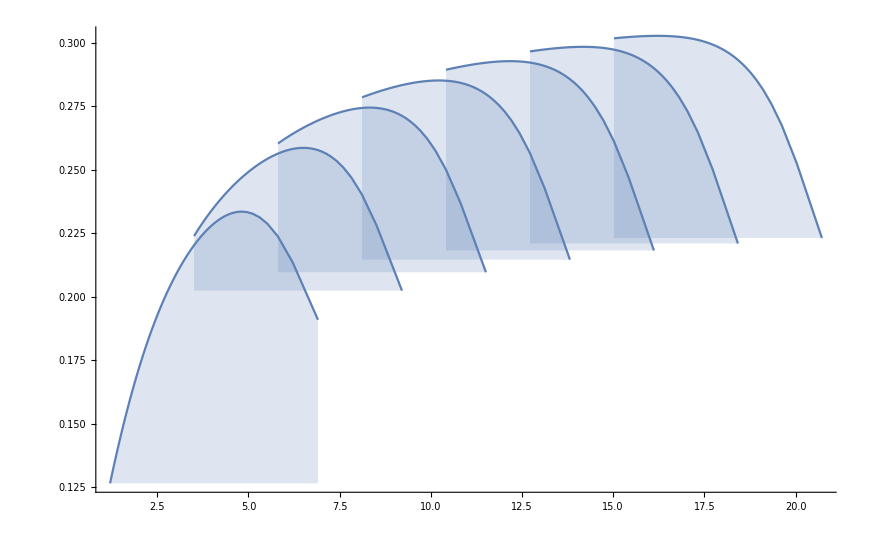

```mathematica
Table[Table[{Log[1/tb[300,m]⟦i,1⟧],1/m tb[300,m]⟦i,1⟧(tb[300,m]⟦i+1,2⟧-tb[300,m]⟦i,2⟧)},{i,Length@tb[300,m]-1}]//ListPlot[#,Joined->True, Filling->Bottom, PlotRange->All]&,{m,masses}]//Drop[#,1]&//Show[#,PlotRange->All]&
```

Following the tip of the iceberg:

```mathematica
Do[𝕗[m]=Interpolation@Table[{tb[300,m]⟦i,1⟧,1/m tb[300,m]⟦i,1⟧(tb[300,m]⟦i+1,2⟧-tb[300,m]⟦i,2⟧)},{i,Length@tb[300,m]-1}],{m,masses}]
```

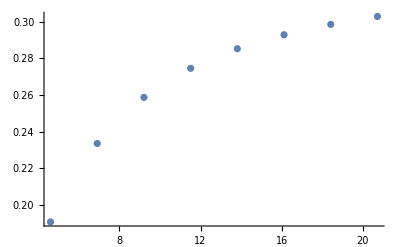

```mathematica
(max=Table[{Log[1/m],FindMaximum[𝕗[m][x],{x,100 m}]⟦1⟧//Quiet},{m,masses}])//ListPlot[#,PlotRange->All]&
```

```mathematica
Fit[max,{1,1/x,1/x^2,1/x^3,1/x^4,1/x^5},x]
```

0.333301+59.0529/x^5-56.775/x^4+22.3983/x^3-3.45686/x^2-0.511536/x

1/3 as expected!